## Quantity/Unit Convenience

### UnitForm: Postfix friendly UnitConvert

```mathematica
UnitForm[units_][quantity_]:=UnitConvert[quantity,units]
UnitForm::usage="like UnitConvert but for postfix";
```

```mathematica
(* Make it so you can always UnitForm 0 into any units *)
(*UnitConvert[zero_?(#==0&),targetunit_]^:=Quantity[0,targetunit]*)
(*UnitConvert[0.,targetunit_]^:=Quantity[0,targetunit]*)
```

#### Example usage

```mathematica
Quantity[10,"Meters/Second"]//N@*UnitForm["mph"]
```

22.3694 mi/h

### ("unit")_q: Interpret a string as a quantity with subscript q

```mathematica
Subscript[s_String, q]:=Quantity[s]
```

#### Example usage

```mathematica
10 Subscript["mph", q]
```

10 mi/h

### loadQuantities: Load common physical quantities, both into the input of the function and globally

```mathematica
ClearAll@loadQuantities;
quantityAssoc[HoldPattern@symb]:=<|ℏ->Quantity["ReducedPlanckConstant"]|>[symb]
(* Makes loadQuantities idempotent, so loadQuantities[loadQuantities[ℏ]]==loadQuantities[ℏ] *)
loadQuantities[q_Quantity]:=q;
(* Define constants that can be loaded *)
loadQuantities[HoldPattern@ℏ]:=ℏ=Quantity["ReducedPlanckConstant"];
loadQuantities[HoldPattern[h]]:=h=Quantity["PlanckConstant"];
loadQuantities[HoldPattern@c]:=c=Quantity["SpeedOfLight"];
loadQuantities[HoldPattern@Subscript[q, e]]:=Subscript[q, e]=Quantity["ElectronCharge"];
loadQuantities[HoldPattern@Subscript[m, e]]:=Subscript[m, e]=Quantity["ElectronMass"];
loadQuantities[HoldPattern@Subscript[m, p]]:=Subscript[m, p]=Quantity["ProtonMass"];
loadQuantities[HoldPattern@Subscript[m, n]]:=Subscript[m, n]=Quantity["NeutronMass"];
loadQuantities[HoldPattern@Subscript[m, μ]]:=Subscript[m, μ]=Quantity["MuonMass"];
loadQuantities[HoldPattern@Subscript[m, τ]]:=Subscript[m, τ]=Quantity["TauMass"];
loadQuantities[HoldPattern@Subscript[ϵ, 0]]:=Subscript[ϵ, 0]=Quantity["VacuumPermittivity"];
loadQuantities[HoldPattern@Subscript[μ, 0]]:=Subscript[μ, 0]=Quantity["VacuumPermeability"];
loadQuantities[HoldPattern@Subscript[a, 0]]:=Subscript[a, 0]=Quantity["BohrRadius"];
loadQuantities[HoldPattern@G]:=G=Quantity["GravitationalConstant"];
loadQuantities[HoldPattern@Subscript[N, A]]:=Subscript[N, A]=Quantity["AvogadroConstant"];
loadQuantities[HoldPattern@Subscript[k, B]]:=Subscript[k, B]=Quantity["BoltzmannConstant"];
(* Allow list of quantities to be loaded  *)
SetAttributes[loadQuantities,Listable]
(*(* Handle other symbols not defined above, and return 0 *)
loadQuantities::unknownSymb="Unknown symbol `1`";
loadQuantities[symb_]:=(Message[loadQuantities::unknownSymb,symb];symb);*)
(* Return unknown symbols unchanged *)
loadQuantities[symb_]:=symb;
(* Load product, sum, etc of constants at once *)
loadQuantities[HoldPattern[f_[symbs__]]]:=f@@loadQuantities[{symbs}]
(* Allow list of quantities to be loaded without surrounding in brackets *)
loadQuantities[symbs__]:=loadQuantities[{symbs}]
(* With no arguments, load all quantities *)
(* todo figure out how to not have to hardcode the -5 (# of non-definition defs) *)
loadQuantities[]:=(Keys[DownValues[loadQuantities]]/.loadQuantities->List)[[;;-5,1]]//Flatten//ReleaseHold//loadQuantities
```

#### Example usage:

Load some quantities, then use them

```mathematica
loadQuantities[Subscript[μ, 0],Subscript[q, e],ℏ,Subscript[m, e],Subscript[a, 0]]
(Subscript[μ, 0] Subscript[q, e] ℏ)/(4π Subscript[m, e] Subscript[a, 0]^3)//UnitForm@"Teslas"
Subscript[μ, 0]=.
Subscript[q, e]=.
ℏ=.
Subscript[m, e]=.
Subscript[a, 0]=.
```

{ μ_0, e, ℏ, m_e, a_0}

12.516824 T

Load needed quantities in an expression, and then re-use them

```mathematica
loadQuantities[(Subscript[μ, 0] Subscript[q, e] ℏ)/(4π Subscript[m, e] Subscript[a, 0]^3)]//UnitForm@"Teslas"
Subscript[m, e] loadQuantities[c^2]//UnitForm@"keV"
Subscript[μ, 0]=.
Subscript[q, e]=.
ℏ=.
Subscript[m, e]=.
Subscript[a, 0]=.
c=.
```

12.516824 T

510.99895 keV

Load all quantities, then use them

```mathematica
loadQuantities[]
(Subscript[μ, 0] Subscript[q, e] ℏ)/(4π Subscript[m, e] Subscript[a, 0]^3)
```

{ c, G, h, ℏ, a_0, k, m_e, m_n, m_p, m_μ, m_τ, N_A, e, ε_0, μ_0}

1/(4 π) e μ_0 ℏ/(m_e a_0^3)

## Side Effects

Useful when you want to keep the value of some expression, but also do something else with it (print it, save it, etc)

### also: Do something as a side effect

```mathematica
also[f_][x_]:=(f@x;x)
```

#### Example usage:

```mathematica
x={2}
y=RandomInteger[10]//also[AppendTo[x,#]&]
x
```

{2}

8

{2,8}

### alsoPrint: Print some thing as a side effect

```mathematica
alsoPrint[f_:Identity]:=also[Print@*f]
```

#### Example usage:

```mathematica
A=RandomInteger[10,{4,4}]//alsoPrint@MatrixForm;
N@Eigenvalues@A
```

(5 | 4 | 10 | 10
6 | 9 | 10 | 6
4 | 4 | 2 | 3
5 | 7 | 2 | 9)

{23.9211,-4.00935,2.54412+1.76634 ⅈ,2.54412-1.76634 ⅈ}

### save, alsoSave: Save a figure as png or svg (as a side effect)

```mathematica
saveDirectory[]:=Module[
	{dir=FileNameJoin@{NotebookDirectory[],"mathematica_figures"}},
	If[
		!DirectoryQ@dir,
		CreateDirectory[FileNameJoin@{NotebookDirectory[],"mathematica_figures"}],
		dir
	]
]
save[fig_,name_String,format_String:"pdf",dpi_Integer:500]:=Export[FileNameJoin@{saveDirectory[],name<>"."<>format},fig,ImageResolution->dpi]
save[fig_,name_String,formats_List,dpi_Integer:500]:=save[fig,name,#,dpi]&/@formats
alsoSave[name_String,format_String:"pdf",dpi_Integer:500]:=also[save[#,name,format,dpi]&]
alsoSave[name_String,formats_List,dpi_Integer:500]:=also[save[#,name,formats,dpi]&]
```

### alsoCopy:

```mathematica
alsoCopyOpts[opts___]:=also[CopyToClipboard@Rasterize[#,opts]&];
alsoCopy=alsoCopyOpts[]
```

also[CopyToClipboard[Rasterize[#1]]&]

### tableHeaded: TableForm but with headers

```mathematica
tableHeaded[headers_][list_]:=TableForm[list,TableHeadings->headers]
tableHeadedRows[rows_][list_]:=TableForm[list,TableHeadings->{rows,None}]
tableHeadedCols[cols_][list_]:=TableForm[list,TableHeadings->{None,cols}]
```

```mathematica
a=RandomInteger[5,4];
b=RandomInteger[10,6];
{a,b}//tableHeadedRows[{"a","b"}]
```

a | 4 | 0 | 3 | 5 |  | 
b | 1 | 2 | 10 | 0 | 4 | 2

## Colors

### defaultColorData: Quicker access to the default plot colors

```mathematica
defaultColorData[]:=ColorData[97]
defaultColorData[n_Integer]:=defaultColorData[][n]
```

#### Example usage:

When combining separate plots with Show, this makes it easier to use the right two colors

```mathematica
f=x^2;
data=Table[{x,f+RandomReal[0.5]},{x,0,2,0.2}];
```

```mathematica
plot=Plot[
f,{x,0,2}
];
```

By default, both are this blue color (ColorData[97][1])

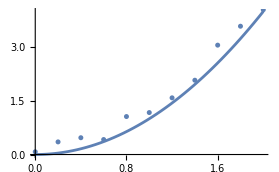

```mathematica
Show[
plot,ListPlot[data]
]
```

To get the same different color as if both were in the same Plot function:

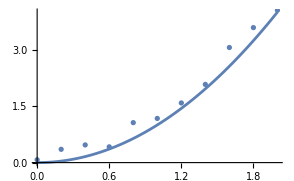

```mathematica
Show[
plot,ListPlot[data,ColorFunction->(defaultColorData[2]&)]
]
```

### Pride Colors!

```mathematica
(* Pride Flags! *)
(* How to add gradients: https://mathematica.stackexchange.com/questions/57885/is-it-possible-to-insert-new-colour-schemes-into-colordata/57893#57893 *)
(* Flag rgb colors: https://www.flagcolorcodes.com/flags/pride *)

ColorData[1];
(* Export this function so users can add gradients as needed *)
insertGradient[name_,gradColors_]:=If[
	!MemberQ[ColorData["Gradients"],name],
	(
		AppendTo[
			DataPaclets`ColorDataDump`colorSchemes,
			{{name,"",{}},{"Gradients"},1,{0,1},gradColors,""}
		];
		AppendTo[
			DataPaclets`ColorDataDump`colorSchemeNames,
			name
		];
	)
]
Module[{data,names,colors},
	data=Import["https://raw.githubusercontent.com/Annie-Schwartz/YouTilities/master/flags.tsv","TSV","Numeric"->False];
	names=#<>"Flag"&/@data[[;;,1]];
	colors=Map[RGBColor["#"<>#]&,data[[;;,2;;]],{2}];
	
	insertGradient@@#&/@Transpose@{names,colors};
]
```

#### List of Gradients:

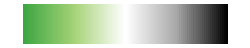
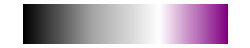
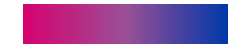
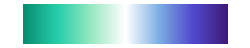
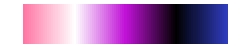
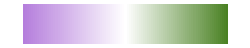
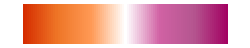
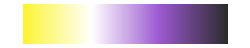
AromanticFlag | -Graphics-
AsexualFlag | -Graphics-
BiFlag | -Graphics-
GayFlag | -Graphics-
GenderfluidFlag | -Graphics-
GenderqueerFlag | -Graphics-
LesbianFlag | -Graphics-
NonbinaryFlag | -Graphics-
NWAromanticFlag | -Graphics-
NWAsexualFlag | -Graphics-
NWGayFlag | -Graphics-
NWGenderfluidFlag | -Graphics-
NWGenderqueerFlag | -Graphics-
NWLesbianFlag | -Graphics-
NWNonbinaryFlag | -Graphics-
NWTransFlag | -Graphics-
OmniFlag | -Graphics-
PanFlag | -Graphics-
PrideFlag | -Graphics-
TransFlag | -Graphics-

```mathematica
With[{data=Select[StringEndsQ@"Flag"]@ColorData@"Gradients"},
TableForm[
ColorData[#,"Image"]&/@data,
TableHeadings->{data,None}
]
]
```

#### Example usage:

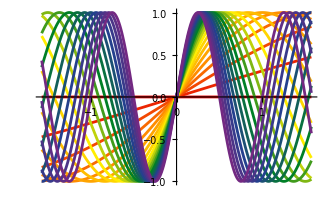

```mathematica
Table[Sin[n π x],{n,0,2,0.1}];
Plot[
%,
{x,-π/2,π/2},
PlotStyle->"PrideFlag"
]
```

## Linear Algebra

### EigvecsT, EigsysT: Wrapper for melt’s functions to allow for getting the eigenvectors as lists of lists, rather than a matrix (row-major vs col-major)

```mathematica
Thread[f[{a,b},{c,d}]]
```

{f[a,c],f[b,d]}

```mathematica
EigvecsT[A_,neigs_:"all",Δ_:Automatic]:=Transpose@Eigvecs[A,neigs,Δ]
EigsysT[A_,neigs_:"all",Δ_:Automatic]:=MapThread[#1@#2&,{{Identity,Transpose},Eigsys[A,neigs,Δ]}]
```

#### Example Usage:

```mathematica
<<http://www.fmt.if.usp.br/~gtlandi/download/melt.m
(* Eigenvalues of a spin 3/2 Hamiltonian *)
LoadArbitrarySpinMatrices[3/2];
H = Sz + 0.3 Sx.Sx//mf;
```

(1.725 | 0 | 0.259808 | 0
0 | 1.025 | 0 | 0.259808
0.259808 | 0 | 0.025 | 0
0 | 0.259808 | 0 | -1.275)

```mathematica
eigenStuff[H]
```

λ | Eigenvector
1.76382 | (0.989021
0.
0.147776
0.)
-1.30398 | (0.
-0.110866
0.
0.993835)
1.05398 | (0.
-0.993835
0.
-0.110866)
-0.0138194 | (0.147776
0.
-0.989021
0.)

```mathematica
EigsysT@H
```

{{-1.30398,-0.0138194,1.05398,1.76382},{{0.,-0.110866,0.,0.993835},{0.147776,0.,-0.989021,0.},{0.,-0.993835,0.,-0.110866},{0.989021,0.,0.147776,0.}}}

```mathematica
eigenStuff[H,sys->EigsysT]
```

λ | Eigenvector
-1.30398 | (0.
-0.110866
0.
0.993835)
-0.0138194 | (0.147776
0.
-0.989021
0.)
1.05398 | (0.
-0.993835
0.
-0.110866)
1.76382 | (0.989021
0.
0.147776
0.)

```mathematica
EigvecsT[H]//tableHeadedCols[{"v_1","v_2","v_3","v_4"}]
```

v_1 | v_2 | v_3 | v_4
0. | -0.110866 | 0. | 0.993835
0.147776 | 0. | -0.989021 | 0.
0. | -0.993835 | 0. | -0.110866
0.989021 | 0. | 0.147776 | 0.

### M_mp^n: Exponentiate matrices with correct matrix multiplication

Todo: make a more general version that works with kron too I think makes the most sense

```mathematica
(* Exponentiate with something other than Times (useful for matrix powers with Dot) *)
Subscript/:Power[Subscript[mat_,mp],n_]:=MatrixPower[mat,n]
Subscript/:Power[Subscript[mat_,Dot],n_]:=MatrixPower[mat,n]
```

#### Example usage:

```mathematica
A=PauliMatrix[1]//alsoPrint@MatrixForm;
```

(0 | 1
1 | 0)

The normal exponentiation behavior is to multiply element-wise

```mathematica
Table[MatrixForm[A^n],{n,3}]
```

{(0 | 1
1 | 0),(0 | 1
1 | 0),(0 | 1
1 | 0)}

Using this gets the correct matrix multiplication n times

```mathematica
Table[MatrixForm[Subscript[A, mp]^n],{n,3}]
```

{(0 | 1
1 | 0),(1 | 0
0 | 1),(0 | 1
1 | 0)}

Another common use case, with melt’s kron function

```mathematica
Subscript/:Power[Subscript[mat_,f_],n_Integer]:=f@@Table[mat,n]/;(Print[DownValues@f];False)
```

```mathematica
kron[mats__]:=KroneckerProduct[mats];
CircleTimes[things__]:=kron[things];
```

```mathematica
Definition[Dot]
```

Attributes[Dot]={Flat,OneIdentity,Protected}

```mathematica
<<https://raw.githubusercontent.com/szhorvat/Spelunking/master/Spelunking.m
```

```mathematica
Spelunk[Dot]
```

Attributes[Dot]={Flat,OneIdentity}

```mathematica
Subscript[A, Dot]^2
```

{{1,0},{0,1}}

```mathematica
Dimensions[Subscript[A, kron]^2]
```

{2}

### eigenStuff: Make a nice lil table of eigenvalues & vectors

matrix: The matrix to calculate the eigenvalues & vectors for
sys: The function used to get the eigens. Must return a tuple of {vals,vecs} Defaults to Eigensystem, but is configurable (mostly for use with melt’s Eigsys for sorting)
aiλ: Whether to show a column for A-Iλ
rref: Whether to show a column for the reduced row echelon form
normalize: Whether to normalize the eigenvectors

```mathematica
ClearAll@eigenStuff
eigenStuff::zeroEigenvectors="Some zero-eigenvectors";
eigenStuff::unequal="#vals!=#vecs";
eigenStuff[matrix_,opts:OptionsPattern[{sys->Eigensystem,aiλ->False,rref->False,normalize->False}]]:=Module[
	{
		aiλ=OptionValue@aiλ,
		rref=OptionValue@rref,
		normalize=OptionValue@normalize,
		sys=OptionValue@sys,
		len=Length@matrix,
		vecs,vals
	},
	{vals,vecs}=sys[matrix];
	vecs=If[normalize,Normalize/@vecs,vecs];
	If[ContainsAny[vecs,{Table[0,len]}],
		Throw[Message[eigenStuff::zeroEigenvectors]]
	];
	AIλ=matrix-# IdentityMatrix@len&/@vals//Simplify;
	If[Length/@{vals,vecs}/.List->Equal,
		Grid[
			Join[
				{{"λ",If[aiλ,"A-Iλ",Nothing],If[rref,"RREF",Nothing],"Eigenvector"}},
				{
					vals,
					If[aiλ,MatrixForm/@AIλ,Nothing],
					If[rref,MatrixForm@*RowReduce/@AIλ,Nothing],
					MatrixForm/@vecs
				}ᵀ
			],
			Frame->All
		],
		Message[eigenStuff::unequal]
	]
]
```

```mathematica
A=RandomInteger[10,{4,4}];
```

```mathematica
eigenStuff[A,rref->False,aiλ->False,normalize->True,sys->Eigsys]//N
```

λ | Eigenvector
-7.04733 | (-0.775882
0.0941402
-0.334806
-0.526355)
-2.64597 | (0.249192
0.36187
0.569483
-0.694725)
4.47617 | (0.328695
-0.729094
0.463801
-0.381144)
19.2171 | (0.509951
0.233938
-0.650125
-0.512407)

### hc (and cc): Add the Hermitian (complex) conjugate of a matrix (value) to itself

```mathematica
CirclePlus[mat_?MatrixQ,hc]:=mat+mat†
CirclePlus[val_,cc]:=val+val*
```

```mathematica
mat={{1, 0, 2}, {0, 1, 0}, {0, 0, 0}};
mat+mat†//MatrixForm
mat⊕hc//MatrixForm
```

(2 | 0 | 2
0 | 2 | 0
2 | 0 | 0)

(2 | 0 | 2
0 | 2 | 0
2 | 0 | 0)

### LoadBra: Defines Bra as the complex conjugate of Ket of the same things

```mathematica
LoadBra[]:=(
labels__:=labels*;
a__b__:=a*.b;
)
```

#### Example usage:

```mathematica
n_:={n,ⅈ,n+ⅈ}
2
2
```

{2,ⅈ,2+ⅈ}

{2,-ⅈ,2-ⅈ}

```mathematica
LoadBra[]
2
2
22
```

{2,ⅈ,2+ⅈ}

{2,-ⅈ,2-ⅈ}

6+4 ⅈ

### LoadArbitrarySpinMatricesJ: Melt’s LoadArbitrarySpinMatrices but defining Jx, etc. instead of Sx

```mathematica
?LoadArbitrarySpinMatrices
```

```mathematica
LoadArbitrarySpinMatricesJ[S_,type_:"n",chain_:1]:=If[Length@DownValues@LoadArbitrarySpinMatrices==0,
"Please make sure to load Melt before running LoadArbitrarySpinMatricesJ!",
(*{J0,Jx,Jy,Jz,Jp,Jm,𝒥x,𝒥y,𝒥z,𝒥p,𝒥m}=Eat[{S0,Sx,Sy,Sz,Sp,Sm,𝒮x,𝒮y,𝒮z,𝒮p,𝒮m},LoadArbitrarySpinMatrices[S,type,chain]];*)
Block[{S0,Sx,Sy,Sz,Sp,Sm,𝒮x,𝒮y,𝒮z,𝒮p,𝒮m},
ClearAll[J0,Jx,Jy,Jz,Jp,Jm];
LoadArbitrarySpinMatrices[S,type,chain];
J0=S0;Jx=Sx;Jy=Sy;Jz=Sz;Jp=Sp;Jm=Sm;
If[chain===1,
"Matrices loaded: J0 (=1), Jx, Jy, Jz, Jp, Jm",
𝒥0=𝒮0;𝒥x=𝒮x;𝒥y=𝒮y;𝒥z=𝒮z;𝒥p=𝒮p;𝒥m=𝒮m;"Matrices loaded: 𝒥0 (=1), 𝒥x, 𝒥y, 𝒥z, 𝒥p, 𝒥m"
]
]
]
```

```mathematica
LoadArbitrarySpinMatricesJ[5]
```

Please make sure to load Melt before running LoadArbitrarySpinMatricesJ

### BlockDiagonalizer: Construct a unitary to block diagonalize according to some symmetry (i.e. operator)

```mathematica
ClearAll[BlockDiagonalizer]
BlockDiagonalizer[ops__]:=Module[{os=Reverse@{ops},U},
U=BlockDiagonalizer@First@os;
Do[
U=U.BlockDiagonalizer[Inverse[U].os[[idx]].U],
{idx,2,Length@os}
];
U
]
BlockDiagonalizer[op_]:=LocalizeAll[{},{},
{λs,vs}=Eigensystem@op;
Transpose@vs[[Ordering[λs,All,Greater]]]
]
(*BlockDiagonalizer[op_]:=LocalizeAll[{},{},
{λs,vs}=Eigensystem@op;
evals=Sort[DeleteDuplicates@λs,Greater];
Transpose@flat1@Table[
Normalize/@vs[[Flatten@Position[λs,λ]]],
{λ,evals}
]
]*)
```

#### Example Usage

The following model of two coupled spins:

```mathematica
<<C:\Users\annie\Documents\Rochester\Research\melt.m
```

```mathematica
LoadArbitrarySpinMatricesJ[j=2,"a"];
𝒥0=J0⊗J0;
{𝒥x,𝒥y,𝒥z}=Table[
kron@@Basis[2,idx]/.{1->op,0->J0},
{op,{Jx,Jy,Jz}},
{idx,2}
];
ℋ[x_]:=-x Total@𝒥z-(1-x)/(4j)Subscript[Total[𝒥x], mp]^2
```

conserves parity (Π) and total spin 𝒥2:

```mathematica
Π=Chop@MatrixExp[ⅈ π (Jz-j J0)];
𝒥2=Subscript[Total[𝒥x], mp]^2+Subscript[Total[𝒥y], mp]^2+Subscript[Total[𝒥z], mp]^2//Chop;
ℂ[ℋ[x],Π⊗Π]//Simplify//MatrixForm
Map[Chop@*Simplify,ℂ[ℋ[x],𝒥2],{2}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Thus, we can find a unitary matrix U that simultaneously (block) diagonalizes ℋ (or anything else that commutes with Π and 𝒥2) into blocks of definite parity and total spin:

```mathematica
U=BlockDiagonalizer[𝒥2,Π⊗Π];
Ui=Inverse@U;
Dimensions@U
Ui.(Π⊗Π).U//Chop//MatrixForm
Ui.ℋ[x].U//Simplify//Chop//MatrixForm
Ui.ℋ[1].U//Chop//MatrixForm
Ui.ℋ[0].U//Chop//MatrixForm
```

{25,25}

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(1/4 (-1-15 x) | (7 (-1+x))/(4 √6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/8 √(3/2) (-1+x) | -1-x | 15/8 √(3/2) (-1+x) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/8 √(3/2) (-1+x) | 5/4 (-1+x) | 1/8 √(3/2) (-1+x) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 15/8 √(3/2) (-1+x) | -1+3 x | 1/8 √(3/2) (-1+x) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (7 (-1+x))/(4 √6) | 1/4 (-1+17 x) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/16 (-11-37 x) | 21/16 (-1+x) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3/16 (-1+x) | 1/16 (-19+3 x) | 5/8 (-1+x) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 5/8 (-1+x) | 1/16 (-19+35 x) | 3/16 (-1+x) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 21/16 (-1+x) | 1/16 (-11+59 x) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-1-3 x) | 5/8 √(3/2) (-1+x) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 √(3/2) (-1+x) | 3/4 (-1+x) | 1/8 √(3/2) (-1+x) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5/8 √(3/2) (-1+x) | 1/2 (-1+5 x) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3/16 (1+15 x) | 5/16 (-1+x) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3/16 (-1+x) | 1/16 (-11-5 x) | 3/8 (-1+x) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3/8 (-1+x) | 1/16 (-11+27 x) | 3/16 (-1+x) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5/16 (-1+x) | 3/16 (-1+17 x) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 (-1-15 x) | 1/8 √(3/2) (-1+x) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 √(3/2) (-1+x) | 3/8 (-1+x) | 1/8 √(3/2) (-1+x) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 √(3/2) (-1+x) | 1/8 (-1+17 x) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/16 (-5-11 x) | 3/16 (-1+x) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3/16 (-1+x) | 1/16 (-5+21 x) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 (-1+x) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/16 (-1-15 x) | 1/16 (-1+x) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/16 (-1+x) | 1/16 (-1+17 x) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(-4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(-1/4 | -(√(3/2))/4-1/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(√(3/2))/8 | -1 | -(15 √(3/2))/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(√(3/2))/8 | -5/4 | -(√(3/2))/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -(15 √(3/2))/8 | -1 | -(√(3/2))/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(√(3/2))/4-1/(√6) | -1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -11/16 | -21/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -3/16 | -19/16 | -5/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -5/8 | -19/16 | -3/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -21/16 | -11/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | -(5 √(3/2))/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(√(3/2))/8 | -3/4 | -(√(3/2))/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(5 √(3/2))/8 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3/16 | -5/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3/16 | -11/16 | -3/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3/8 | -11/16 | -3/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5/16 | -3/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/8 | -(√(3/2))/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(√(3/2))/8 | -3/8 | -(√(3/2))/8 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(√(3/2))/8 | -1/8 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5/16 | -3/16 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3/16 | -5/16 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/8 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/16 | -1/16 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/16 | -1/16 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Note that the order of symmetries is important! The above is first block diagonalized by total spin, the below first block diagonalizes by parity:

```mathematica
U=BlockDiagonalizer[Π⊗Π,𝒥2];
Ui=Inverse@U;
Ui.ℋ[x].U//Simplify//MatrixForm
Ui.ℋ[1].U//MatrixForm
```

(-0.273693-0.00597489 x | 0.0534048-0.0504194 x | 0.2155-0.389488 x | -0.154653+0.346356 x | 0.104602+0.392883 x | -0.118489-0.235332 x | 0.0785508+0.566354 x | 0.161182-0.161182 x | 0.0809446-0.0809446 x | 0.00324852+0.0158644 x | -0.0690027+0.091049 x | 0.17366-0.17366 x | -0.114423+0.521936 x | -3.04465×10^-17+2.88022×10^-16 x | -9.58128×10^-17+1.95252×10^-16 x | -1.04923×10^-16+1.04025×10^-16 x | 3.5924×10^-17+3.35789×10^-17 x | -7.09403×10^-17-2.20696×10^-16 x | -1.20622×10^-16+9.49129×10^-17 x | -1.04265×10^-17-1.05791×10^-16 x | -1.10504×10^-16+1.10504×10^-16 x | -2.98457×10^-17+1.44865×10^-16 x | -3.95998×10^-18-4.00869×10^-16 x | 5.21997×10^-17-2.01575×10^-17 x | -8.0927×10^-18-2.25128×10^-16 x
0.0763171-1.29286 x | -0.550014-0.679661 x | -0.251191+0.411639 x | -0.028738+0.335876 x | 0.142862-0.660601 x | -0.0650065+0.907442 x | 0.0899565-0.808635 x | -0.039615+0.039615 x | -0.054744+0.054744 x | -0.00165479-0.0559746 x | -0.125976-0.161264 x | -0.31128+0.31128 x | 0.268877-0.529459 x | -2.39124×10^-17-1.19762×10^-16 x | 1.25667×10^-16-4.2423×10^-16 x | -1.10458×10^-17+1.39714×10^-17 x | -4.58116×10^-18-6.88024×10^-17 x | 4.60787×10^-17+3.73478×10^-16 x | 8.09659×10^-17-1.61683×10^-16 x | 1.83416×10^-17+1.16387×10^-16 x | 6.24688×10^-17-6.24688×10^-17 x | -5.61225×10^-17+1.50135×10^-17 x | 1.97188×10^-18+4.40467×10^-16 x | -3.21545×10^-17-6.55282×10^-17 x | -2.04203×10^-17+5.22551×10^-17 x
0.0860899+2.17644 x | -1.51019+2.56101 x | -1.15527+0.210365 x | -0.354941-0.0624249 x | 0.231822+0.225976 x | -0.551118-0.463775 x | 0.317509+0.0803186 x | -0.293363+0.293363 x | 0.140342-0.140342 x | -0.302004+0.319026 x | -0.568069-0.180271 x | -0.151039+0.151039 x | -0.490181-0.0354909 x | -2.59112×10^-16+3.44736×10^-16 x | 6.00287×10^-17+2.28002×10^-16 x | -1.47228×10^-16-3.89344×10^-19 x | 5.73318×10^-17-2.63383×10^-17 x | 3.79351×10^-16-1.88317×10^-15 x | 1.42044×10^-16-3.7665×10^-16 x | -5.22878×10^-17-2.15741×10^-16 x | -7.08243×10^-17+7.08243×10^-17 x | -2.15957×10^-16+1.2907×10^-16 x | 2.2058×10^-16-1.10185×10^-15 x | -6.00138×10^-17+2.42153×10^-16 x | 3.44107×10^-16-5.06434×10^-16 x
-0.376702+4.58254 x | -2.68065+4.93533 x | -1.13589+0.400658 x | -0.973985+0.277126 x | 0.81926+0.55071 x | -0.841493-0.555557 x | 0.337546+1.58215 x | -0.375944+0.375944 x | 0.226336-0.226336 x | -0.573782-1.08588 x | -1.17641+1.07779 x | -0.121929+0.121929 x | -1.00798+0.972068 x | -4.26273×10^-16-2.20712×10^-16 x | 2.29154×10^-16-7.46485×10^-17 x | -2.10716×10^-16-5.02818×10^-16 x | 8.35824×10^-17+8.89458×10^-17 x | 4.63315×10^-16-2.17926×10^-15 x | 7.99065×10^-17+1.82625×10^-16 x | -8.85647×10^-17-1.11903×10^-16 x | -5.9947×10^-17+5.9947×10^-17 x | -4.2707×10^-16+3.13196×10^-17 x | 3.81548×10^-16+1.62406×10^-18 x | 2.05977×10^-17+1.82906×10^-16 x | 4.23208×10^-16-7.59185×10^-16 x
0.376456+0.26938 x | 0.0344746-0.275051 x | -0.482276-0.526763 x | 0.218075+0.309229 x | -0.430745+1.02059 x | 0.013014-0.0789511 x | 0.0374153+0.279811 x | -0.0982371+0.0982371 x | 0.0532977-0.0532977 x | 0.0379049-0.423147 x | 0.190352-0.124273 x | -0.125603+0.125603 x | 0.187028-0.425621 x | 2.21546×10^-17+2.45028×10^-17 x | 6.36168×10^-17+1.26979×10^-17 x | -3.19311×10^-17-2.32666×10^-17 x | 2.46761×10^-17-3.31046×10^-17 x | 6.15634×10^-17-2.21421×10^-16 x | 1.43186×10^-16-2.26885×10^-16 x | 1.15762×10^-17+2.73492×10^-17 x | 3.16999×10^-17-3.16999×10^-17 x | -6.05791×10^-18-5.77453×10^-17 x | -3.29511×10^-17-1.61658×10^-17 x | -4.773×10^-17-1.24065×10^-16 x | 4.96032×10^-17+4.55471×10^-16 x
0.257691-2.37419 x | 1.24637-2.13829 x | 0.288221+0.185608 x | 0.452524-0.349354 x | -0.414358-0.427514 x | 0.121636+0.313519 x | 0.0894637-1.17653 x | 0.204838-0.204838 x | -0.100733+0.100733 x | 0.158705+1.11552 x | 0.577391-0.791015 x | -0.0198453+0.0198453 x | 0.548982-0.548692 x | 1.85716×10^-16+2.38564×10^-16 x | -7.63196×10^-17+1.04623×10^-16 x | 9.804×10^-17+2.88821×10^-16 x | -2.32583×10^-17-8.43786×10^-17 x | -1.65482×10^-16+7.82633×10^-16 x | 3.32271×10^-17-2.46357×10^-16 x | 4.21992×10^-17+9.06231×10^-17 x | -1.3207×10^-19+1.3207×10^-19 x | 1.99769×10^-16-2.95183×10^-17 x | -1.69609×10^-16-1.36196×10^-16 x | -7.39219×10^-17-1.9893×10^-16 x | -1.22498×10^-16+9.74654×10^-16 x
0.0926948-0.222728 x | 0.389298-1.53862 x | 0.340952-1.09212 x | 0.15259+0.332186 x | -0.245879+0.759857 x | 0.507478-0.367876 x | -0.757999+1.26518 x | -0.131367+0.131367 x | 0.176458-0.176458 x | 0.0914516-0.876949 x | 0.404188-1.37083 x | 0.424974-0.424974 x | -0.435849+0.248701 x | 6.28059×10^-17+1.13111×10^-16 x | -2.42903×10^-17+4.29893×10^-16 x | 1.62198×10^-18+6.87042×10^-19 x | -5.92414×10^-17+1.28549×10^-16 x | -8.60779×10^-17+9.21506×10^-17 x | -7.82865×10^-17+7.30963×10^-17 x | -3.83843×10^-17+2.399×10^-17 x | 1.67225×10^-17-1.67225×10^-17 x | 8.15648×10^-17-3.80674×10^-16 x | 1.69795×10^-17+4.46494×10^-16 x | 4.83609×10^-17-7.71624×10^-17 x | -4.32334×10^-17-6.70327×10^-16 x
0.148034-0.148034 x | -0.088561+0.088561 x | -0.165851+0.165851 x | 0.0606266-0.0606266 x | 0.00453194-0.00453194 x | 0.0571104-0.0571104 x | -0.0764737+0.0764737 x | -0.25-3.75 x | 0. | -0.0673523+0.0673523 x | -0.0547571+0.0547571 x | -1.72581×10^-18+1.72581×10^-18 x | -0.138928+0.138928 x | -1.05285×10^-17+1.05285×10^-17 x | 3.27942×10^-17-3.27942×10^-17 x | -2.35738×10^-17+2.35738×10^-17 x | 4.63688×10^-19-4.63688×10^-19 x | 2.89907×10^-17-2.89907×10^-17 x | 1.94108×10^-17-1.94108×10^-17 x | -5.61199×10^-18+5.61199×10^-18 x | 0. | -5.64393×10^-17+5.64393×10^-17 x | 3.79825×10^-17-3.79825×10^-17 x | 7.38076×10^-18-7.38076×10^-18 x | 1.2338×10^-17-1.2338×10^-17 x
0.0416814-0.0416814 x | -0.033597+0.033597 x | -0.0748303+0.0748303 x | 0.0123284-0.0123284 x | 0.162218-0.162218 x | -0.104694+0.104694 x | 0.216326-0.216326 x | 0. | -0.25+4.25 x | -0.109063+0.109063 x | -0.158496+0.158496 x | -0.153093+0.153093 x | 0.078711-0.078711 x | -5.91773×10^-19+5.91773×10^-19 x | 1.75308×10^-17-1.75308×10^-17 x | -2.30086×10^-17+2.30086×10^-17 x | 1.39592×10^-17-1.39592×10^-17 x | -1.44615×10^-17+1.44615×10^-17 x | -1.70755×10^-17+1.70755×10^-17 x | 3.45072×10^-18-3.45072×10^-18 x | -1.69967×10^-17+1.69967×10^-17 x | -1.98064×10^-17+1.98064×10^-17 x | 1.70391×10^-17-1.70391×10^-17 x | -2.04681×10^-18+2.04681×10^-18 x | -3.45577×10^-18+3.45577×10^-18 x
-0.147794+0.572544 x | -0.405282-0.157998 x | -0.0615773+0.256112 x | -0.0320412+0.120416 x | 0.279218-0.118886 x | 0.103657+0.533806 x | -0.0844268+0.501149 x | -0.207229+0.207229 x | 0.0480519-0.0480519 x | -0.545786-1.03156 x | 0.0282507-0.199134 x | 0.154027-0.154027 x | -0.587193+0.509513 x | -7.0874×10^-17-3.76941×10^-16 x | 1.09207×10^-16-1.86935×10^-17 x | -8.47577×10^-17-1.78073×10^-16 x | -3.13631×10^-17+5.02127×10^-17 x | -4.05005×10^-19-2.00304×10^-16 x | -9.16426×10^-17+3.1212×10^-16 x | -5.81952×10^-17+1.22986×10^-16 x | 2.46532×10^-17-2.46532×10^-17 x | -8.33561×10^-17-3.38218×10^-16 x | 9.38834×10^-17+1.19741×10^-15 x | 1.01816×10^-16+2.97504×10^-17 x | 3.08933×10^-17-1.20015×10^-15 x
-0.0951396+0.492917 x | -0.181793-0.213872 x | 0.157003-1.18775 x | -0.263625+1.29764 x | 0.262859-0.173629 x | -0.205531+1.13211 x | 0.06654-0.84648 x | -0.10937+0.10937 x | -0.236291+0.236291 x | 0.0858479-0.368672 x | -0.566194+2.19271 x | 0.0457215-0.0457215 x | -0.05767-0.512027 x | -2.4164×10^-17+1.32375×10^-16 x | 8.85055×10^-18+4.23879×10^-17 x | 9.86654×10^-17+1.30087×10^-17 x | 2.17467×10^-17+4.63298×10^-17 x | 5.19178×10^-18+2.68973×10^-16 x | 9.285×10^-19+5.22617×10^-17 x | -1.7019×10^-17+6.01658×10^-17 x | 5.97932×10^-17-5.97932×10^-17 x | 3.33486×10^-17-2.86936×10^-17 x | 7.85669×10^-17-1.18055×10^-16 x | -2.96363×10^-17+2.55222×10^-16 x | 8.07369×10^-18-2.87249×10^-16 x
0.175294+0.247331 x | -0.238571+0.121364 x | -0.270303-0.462414 x | -0.0103702+0.236503 x | 0.108271-0.240858 x | -0.163629+0.0170467 x | 0.245615-0.575885 x | -0.0583805+0.0583805 x | -0.153153+0.153153 x | 0.00716355+0.404128 x | -0.141976+0.00810266 x | -0.408202+2.4082 x | 0.30391-1.00352 x | -1.03072×10^-17+1.10804×10^-16 x | 9.9001×10^-17-8.48405×10^-18 x | 7.23148×10^-17-5.50804×10^-18 x | 3.72085×10^-17+1.00488×10^-17 x | 5.60256×10^-17-1.73925×10^-17 x | 1.27552×10^-16-1.56471×10^-16 x | 1.83767×10^-17-1.09049×10^-16 x | 1.41828×10^-16-3.08054×10^-17 x | 6.07074×10^-17+7.08922×10^-17 x | 1.44836×10^-17-2.27605×10^-16 x | -7.6378×10^-17+6.07586×10^-17 x | 2.19832×10^-17+4.98597×10^-16 x
0.0597998+0.543067 x | -0.00508317-0.0661509 x | -0.040491-0.940294 x | -0.0800504+0.497829 x | -0.0348475+0.288887 x | -0.0492193-0.0150939 x | -0.140078-0.0630458 x | -0.107238+0.107238 x | -0.014589+0.014589 x | 0.101478+0.0612366 x | -0.165498+0.322338 x | 0.171696-0.171696 x | -0.209746-0.220491 x | -5.94853×10^-17-2.9576×10^-18 x | 7.76662×10^-17-1.32259×10^-16 x | 6.03713×10^-17-1.84556×10^-16 x | 4.80221×10^-17+2.47497×10^-18 x | 1.43548×10^-17+5.28917×10^-17 x | 1.13564×10^-16-2.85857×10^-16 x | 2.02168×10^-17+5.07999×10^-17 x | 1.01182×10^-16-1.01182×10^-16 x | 2.02482×10^-17-8.9732×10^-18 x | 6.23039×10^-17-2.95932×10^-16 x | -6.40993×10^-17+1.29221×10^-16 x | -1.10349×10^-17+1.28722×10^-15 x
-1.00462×10^-17+3.1319×10^-16 x | -2.09794×10^-16+3.59455×10^-16 x | -1.43507×10^-16+1.24642×10^-16 x | -3.03384×10^-17+7.24854×10^-18 x | 1.784×10^-17+1.12246×10^-17 x | -5.63961×10^-17-2.84418×10^-17 x | -1.05983×10^-17-8.55198×10^-17 x | -6.21134×10^-17+6.21134×10^-17 x | -3.24204×10^-19+3.24204×10^-19 x | -1.00633×10^-17+4.09123×10^-17 x | -8.33328×10^-17+2.03221×10^-17 x | -3.71729×10^-17+5.64359×10^-17 x | -1.22461×10^-17+1.00517×10^-16 x | -0.343479-0.310982 x | -0.150149-0.38913 x | -0.0177548-0.00172244 x | -0.0912355+0.0912355 x | 0.0911445-0.200452 x | 0.146889-1.11895 x | 0.000490463-0.0733727 x | 0.104144-0.104144 x | -0.0740986+0.4839 x | -0.0677766-1.10872 x | -0.0443241+0.462667 x | -0.0813079-0.900334 x
2.98799×10^-17-1.21527×10^-16 x | 3.89366×10^-17+8.0032×10^-17 x | 1.39989×10^-17+8.29659×10^-17 x | 4.96606×10^-17-1.09263×10^-16 x | -7.90928×10^-18-3.53963×10^-17 x | 7.88794×10^-17-2.29411×10^-16 x | -8.00742×10^-17-4.08923×10^-18 x | 8.69366×10^-18-8.69366×10^-18 x | 2.25297×10^-17-2.25297×10^-17 x | -3.79564×10^-17-2.02535×10^-17 x | 1.20927×10^-17-1.38827×10^-17 x | 5.75987×10^-17-7.47963×10^-17 x | -2.44409×10^-17+1.14879×10^-17 x | -0.200086+0.606616 x | -0.576178+0.928556 x | -0.140593+0.564898 x | 0.128342-0.128342 x | 0.152653-1.66948 x | -0.038494-0.885133 x | -0.0141552+0.138975 x | -0.350987+0.350987 x | -0.274282+0.207375 x | 0.137103-1.77409 x | 0.211524+1.07322 x | -0.187901-0.771463 x
1.32146×10^-16-2.81961×10^-16 x | 6.6509×10^-17-1.69517×10^-16 x | 1.4937×10^-17-7.60001×10^-18 x | -2.61745×10^-17+5.97125×10^-17 x | 4.51428×10^-17-4.44173×10^-17 x | -2.34992×10^-17+9.14414×10^-17 x | -1.83616×10^-17-9.24567×10^-17 x | 5.07673×10^-19-5.07673×10^-19 x | 1.06796×10^-17-1.06796×10^-17 x | 4.00697×10^-17-7.95547×10^-17 x | -3.59827×10^-17+5.9199×10^-17 x | 1.65963×10^-17+4.25543×10^-18 x | -1.6172×10^-17-8.12549×10^-17 x | 0.00275808-0.379899 x | 0.0072076+0.856538 x | -0.859797+0.120181 x | -0.124822+0.124822 x | -0.313453-0.0427663 x | -0.410489+1.15885 x | -0.0327443+0.103999 x | -0.384643+0.384643 x | -0.075261-0.25214 x | -0.112759-0.0264085 x | 0.131368+0.271542 x | -0.00038006+0.287859 x
1.75103×10^-17-3.76405×10^-17 x | -8.2328×10^-17+7.79512×10^-17 x | -1.63669×10^-17+5.07984×10^-17 x | -5.10413×10^-17-8.48436×10^-18 x | 3.32911×10^-17-1.24516×10^-17 x | -2.88556×10^-17-4.99856×10^-17 x | 5.17592×10^-18-1.16923×10^-16 x | -3.0085×10^-17+3.0085×10^-17 x | -2.45871×10^-19+2.45871×10^-19 x | 3.56195×10^-17-1.50248×10^-17 x | -6.15212×10^-17-3.27431×10^-17 x | -8.75523×10^-18+2.57876×10^-17 x | -3.06305×10^-17+1.59309×10^-17 x | -0.0704306-0.755743 x | 0.0149244-0.0870487 x | -0.224+0.23947 x | -0.434457+1.43446 x | 0.0355033-0.167767 x | -0.060815-0.484648 x | -0.0122791+0.085707 x | 0.0137552-0.0137552 x | 0.085371+0.0148905 x | -0.153558-0.419891 x | -0.0833389+0.0670386 x | 0.172507-0.579152 x
-5.2334×10^-17+2.64214×10^-16 x | -1.72741×10^-16+3.82049×10^-16 x | -5.23304×10^-17-7.39478×10^-18 x | -4.90825×10^-17+3.8071×10^-17 x | 5.75745×10^-17-1.97481×10^-17 x | -4.19708×10^-17-1.93801×10^-16 x | -3.9112×10^-17+9.52252×10^-17 x | -4.25126×10^-17+4.25126×10^-17 x | -1.11161×10^-17+1.11161×10^-17 x | -1.18068×10^-17-4.63182×10^-17 x | -7.08447×10^-17+7.4612×10^-17 x | -3.79749×10^-17+3.40315×10^-17 x | -1.76583×10^-17+1.36741×10^-16 x | -0.0876822+0.465752 x | 0.0562799-0.983532 x | -0.0234553-0.174435 x | 0.143194-0.143194 x | -0.236074-1.2263 x | 0.0852809-1.23739 x | 0.0359659-0.105355 x | 0.169363-0.169363 x | -0.0436267+0.379559 x | -0.0386968-0.177708 x | 0.0369739-0.592375 x | -0.111716-0.448695 x
9.58653×10^-17-3.60893×10^-16 x | -2.95644×10^-17+6.60375×10^-17 x | -3.38977×10^-17+2.11696×10^-17 x | -2.46058×10^-17-2.60888×10^-17 x | 1.74886×10^-17-4.11018×10^-17 x | -2.28607×10^-17-2.20344×10^-16 x | 2.54036×10^-17-8.56413×10^-17 x | 5.28547×10^-19-5.28547×10^-19 x | 2.99123×10^-17-2.99123×10^-17 x | 3.51543×10^-17+8.71772×10^-17 x | -2.5799×10^-17-7.85597×10^-17 x | -8.65172×10^-18+1.74868×10^-17 x | 2.88629×10^-18-3.78236×10^-17 x | -0.0288054-0.414338 x | -0.0301469+0.418454 x | -0.411567+0.870381 x | -0.206346+0.206346 x | -0.0437478-0.797033 x | -0.352712+0.434663 x | -0.0206448-0.0512744 x | -0.218892+0.218892 x | 0.0773884-0.282551 x | -0.0498856-0.757454 x | 0.0186317-0.673916 x | 0.153096-0.444979 x
7.92078×10^-17-8.43344×10^-17 x | -3.05019×10^-17+1.41353×10^-16 x | -5.92966×10^-17+1.11333×10^-16 x | -1.28853×10^-17+2.46755×10^-17 x | 6.82488×10^-19+1.71659×10^-17 x | -1.26945×10^-17-2.98512×10^-17 x | 1.42814×10^-18+4.30468×10^-17 x | 3.90572×10^-17-3.90572×10^-17 x | 8.75052×10^-18-8.75052×10^-18 x | 1.95261×10^-17+1.04156×10^-17 x | -5.59738×10^-17+1.4672×10^-16 x | -3.5032×10^-17+3.17381×10^-17 x | -9.94908×10^-18-1.05891×10^-16 x | -0.0874047+0.0942438 x | -0.276121+0.474195 x | -0.322253+0.481593 x | 0.00387752-0.00387752 x | 0.023999-0.0693718 x | -0.162853+0.431672 x | -0.0779962-0.953581 x | -0.380956+0.380956 x | -0.394202+0.398113 x | -0.119673-0.291589 x | 0.165935-0.209159 x | -0.0575442-0.087484 x
1.19184×10^-16-1.13635×10^-16 x | 1.22054×10^-17-2.02181×10^-17 x | -7.48631×10^-17+9.08024×10^-17 x | 3.68756×10^-17-3.78738×10^-17 x | 3.41619×10^-17-3.83181×10^-17 x | 3.69725×10^-17+2.29153×10^-18 x | -6.83172×10^-18+1.01513×10^-17 x | 5.68432×10^-18-5.68432×10^-18 x | -4.71221×10^-18+4.71221×10^-18 x | -3.6406×10^-17+3.1077×10^-17 x | -3.80361×10^-17+5.41787×10^-17 x | -2.68559×10^-19-1.35208×10^-18 x | -4.12794×10^-17+2.71763×10^-17 x | -0.104921+0.268719 x | -0.410652+0.441052 x | -0.350412+0.311701 x | 0.118601-0.118601 x | 0.133916-0.0192399 x | -0.157525+0.30444 x | -0.0118745+0.0535438 x | -1.18987+2.18987 x | -0.47343+0.389477 x | 0.304041-0.103959 x | -0.045085+0.00976848 x | -0.0103271+0.141376 x
4.24856×10^-17-2.55893×10^-16 x | 9.41794×10^-17-1.49304×10^-17 x | -9.51379×10^-18+3.20272×10^-16 x | 6.37832×10^-17-1.53065×10^-16 x | -2.30661×10^-17-1.08733×10^-16 x | 7.11393×10^-17+4.23534×10^-17 x | -2.74579×10^-17-1.84321×10^-17 x | 1.02939×10^-16-1.02939×10^-16 x | -2.67395×10^-17+2.67395×10^-17 x | -4.77211×10^-17+2.06565×10^-16 x | 8.27838×10^-18+1.76911×10^-17 x | -7.64533×10^-17+6.28099×10^-17 x | -4.75638×10^-18+1.21445×10^-16 x | -0.129448+0.227858 x | -0.419824-0.304752 x | -0.20433-0.0704003 x | 0.0814373-0.0814373 x | 0.0641462+0.38468 x | -0.0326161-0.324858 x | 0.000119491-0.0340483 x | -0.475165+0.475165 x | -1.01352+0.180654 x | -0.228117+0.721808 x | 0.378351-0.671415 x | -0.249324+0.284477 x
-1.14699×10^-17-3.44983×10^-17 x | 6.44336×10^-19-8.83675×10^-17 x | 1.78157×10^-17+1.67133×10^-16 x | -1.16557×10^-17-1.21819×10^-17 x | 2.05307×10^-17-1.13784×10^-17 x | 1.13964×10^-18+4.16458×10^-17 x | -2.36197×10^-17+1.9355×10^-17 x | 6.99728×10^-18-6.99728×10^-18 x | -3.38426×10^-17+3.38426×10^-17 x | -3.13209×10^-17-1.33859×10^-16 x | -1.69868×10^-17-7.43914×10^-17 x | -4.62837×10^-17+4.84941×10^-17 x | -5.89624×10^-17+3.49628×10^-16 x | -0.0138534-1.06388 x | 0.102661-1.65224 x | -0.219855-0.715674 x | -0.137297+0.137297 x | -0.211215+0.459118 x | -0.0396565-0.468639 x | -0.0488082+0.261581 x | 0.218216-0.218216 x | -0.284147+0.00563209 x | -0.50955+1.74728 x | 0.268431+0.357684 x | -0.108-0.12218 x
-5.84171×10^-17+5.15639×10^-17 x | -5.78671×10^-17+2.84344×10^-16 x | 2.56873×10^-17+6.9625×10^-17 x | -3.90164×10^-17-3.32806×10^-17 x | 7.2759×10^-17-5.55101×10^-17 x | -3.14236×10^-17-1.31403×10^-16 x | -8.6033×10^-18+2.76027×10^-17 x | -3.74781×10^-17+3.74781×10^-17 x | 3.54786×10^-18-3.54786×10^-18 x | 2.51427×10^-19-1.4628×10^-16 x | -4.29712×10^-18+5.96161×10^-17 x | 1.94425×10^-17-1.24803×10^-17 x | -3.22518×10^-17-4.19858×10^-16 x | -0.164223+0.417034 x | 0.188862+0.957438 x | -0.113591+0.298918 x | -0.0775628+0.0775628 x | -0.0342115-2.15891 x | 0.179238-1.23759 x | -0.0411064+0.188368 x | -0.0933174+0.0933174 x | 0.175268-0.512787 x | 0.172972+0.344451 x | -0.459746-0.844936 x | 0.154854+1.84057 x
-3.373×10^-17+2.43745×10^-16 x | -9.26966×10^-17+3.35628×10^-16 x | -5.18779×10^-17+3.92503×10^-17 x | -3.86646×10^-17-5.87263×10^-17 x | 2.96897×10^-17+5.81272×10^-17 x | -5.59137×10^-17-1.87095×10^-16 x | -3.32909×10^-17+5.23072×10^-17 x | -2.98123×10^-17+2.98123×10^-17 x | 4.16074×10^-18-4.16074×10^-18 x | -4.50521×10^-19+6.69942×10^-18 x | -6.45723×10^-17+9.52984×10^-17 x | 2.42525×10^-17-2.15349×10^-17 x | -2.03161×10^-17-4.37394×10^-16 x | -0.225881-0.317051 x | -0.0568928-0.336547 x | -0.091193+0.142421 x | 0.11632-0.11632 x | -0.00942753-1.24138 x | 0.149551-1.18697 x | 0.0235637-0.095664 x | 0.0185858-0.0185858 x | -0.0821577+0.243141 x | 0.0482615-0.519239 x | -0.012814+0.32071 x | -0.196613+2.55013 x)

(-0.279668 | 0.00298542 | -0.173988 | 0.191704 | 0.497484 | -0.353821 | 0.644905 | 0. | 0. | 0.0191129 | 0.0220463 | -3.06535×10^-16 | 0.407514 | 2.57576×10^-16 | 9.9439×10^-17 | -8.9804×10^-19 | 6.95028×10^-17 | -2.91636×10^-16 | -2.57087×10^-17 | -1.16217×10^-16 | -9.16334×10^-33 | 1.1502×10^-16 | -4.04829×10^-16 | 3.20422×10^-17 | -2.33221×10^-16
-1.21654 | -1.22968 | 0.160449 | 0.307138 | -0.517739 | 0.842436 | -0.718678 | 0. | 0. | -0.0576294 | -0.28724 | 3.24603×10^-16 | -0.260582 | -1.43674×10^-16 | -2.98563×10^-16 | 2.92554×10^-18 | -7.33835×10^-17 | 4.19556×10^-16 | -8.07172×10^-17 | 1.34729×10^-16 | -1.46499×10^-32 | -4.1109×10^-17 | 4.42439×10^-16 | -9.76826×10^-17 | 3.18349×10^-17
2.26253 | 1.05082 | -0.944907 | -0.417366 | 0.457799 | -1.01489 | 0.397827 | 0. | 0. | 0.0170222 | -0.74834 | -2.65956×10^-16 | -0.525672 | 8.56237×10^-17 | 2.88031×10^-16 | -1.47618×10^-16 | 3.09934×10^-17 | -1.50382×10^-15 | -2.34606×10^-16 | -2.68029×10^-16 | -1.61847×10^-32 | -8.68866×10^-17 | -8.81274×10^-16 | 1.82139×10^-16 | -1.62327×10^-16
4.20584 | 2.25467 | -0.735231 | -0.696859 | 1.36997 | -1.39705 | 1.9197 | 0. | 0. | -1.65967 | -0.098626 | -6.96692×10^-16 | -0.0359086 | -6.46985×10^-16 | 1.54506×10^-16 | -7.13534×10^-16 | 1.72528×10^-16 | -1.71594×10^-15 | 2.62531×10^-16 | -2.00468×10^-16 | 7.45109×10^-32 | -3.9575×10^-16 | 3.83172×10^-16 | 2.03504×10^-16 | -3.35976×10^-16
0.645836 | -0.240577 | -1.00904 | 0.527304 | 0.589841 | -0.0659371 | 0.317227 | 0. | 0. | -0.385243 | 0.0660785 | 7.56663×10^-16 | -0.238593 | 4.66574×10^-17 | 7.63147×10^-17 | -5.51977×10^-17 | -8.42849×10^-18 | -1.59858×10^-16 | -8.3699×10^-17 | 3.89254×10^-17 | 4.34933×10^-32 | -6.38032×10^-17 | -4.91169×10^-17 | -1.71795×10^-16 | 5.05075×10^-16
-2.1165 | -0.891919 | 0.473828 | 0.10317 | -0.841872 | 0.435156 | -1.08707 | 0. | 0. | 1.27423 | -0.213624 | 4.52809×10^-16 | 0.000290016 | 4.2428×10^-16 | 2.83031×10^-17 | 3.86861×10^-16 | -1.07637×10^-16 | 6.17151×10^-16 | -2.1313×10^-16 | 1.32822×10^-16 | -4.8269×10^-32 | 1.7025×10^-16 | -3.05805×10^-16 | -2.72852×10^-16 | 8.52156×10^-16
-0.130033 | -1.14932 | -0.751169 | 0.484775 | 0.513977 | 0.139602 | 0.507182 | 0. | 0. | -0.785497 | -0.966638 | -2.97163×10^-16 | -0.187148 | 1.75917×10^-16 | 4.05602×10^-16 | 2.30902×10^-18 | 6.93075×10^-17 | 6.07275×10^-18 | -5.1902×10^-18 | -1.43942×10^-17 | 7.40785×10^-32 | -2.99109×10^-16 | 4.63474×10^-16 | -2.88015×10^-17 | -7.1356×10^-16
0. | 0. | 0. | 0. | 0. | 0. | 0. | -4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.42475 | -0.563281 | 0.194534 | 0.0883749 | 0.160332 | 0.637463 | 0.416722 | 0. | 0. | -1.57735 | -0.170884 | -1.01449×10^-16 | -0.0776802 | -4.47815×10^-16 | 9.05134×10^-17 | -2.62831×10^-16 | 1.88496×10^-17 | -2.00709×10^-16 | 2.20477×10^-16 | 6.47911×10^-17 | 2.46749×10^-32 | -4.21574×10^-16 | 1.29129×10^-15 | 1.31566×10^-16 | -1.16926×10^-15
0.397777 | -0.395664 | -1.03074 | 1.03402 | 0.0892301 | 0.926579 | -0.77994 | 0. | 0. | -0.282824 | 1.62652 | -7.03041×10^-17 | -0.569697 | 1.08211×10^-16 | 5.12384×10^-17 | 1.11674×10^-16 | 6.80765×10^-17 | 2.74165×10^-16 | 5.31902×10^-17 | 4.31468×10^-17 | 8.79454×10^-32 | 4.65507×10^-18 | -3.94883×10^-17 | 2.25586×10^-16 | -2.79175×10^-16
0.422626 | -0.117208 | -0.732717 | 0.226133 | -0.132587 | -0.146583 | -0.33027 | 0. | 0. | 0.411292 | -0.133874 | 2. | -0.699608 | 1.00497×10^-16 | 9.0517×10^-17 | 6.68068×10^-17 | 4.72573×10^-17 | 3.86331×10^-17 | -2.89188×10^-17 | -9.06728×10^-17 | 1.11022×10^-16 | 1.316×10^-16 | -2.13121×10^-16 | -1.56194×10^-17 | 5.2058×10^-16
0.602867 | -0.071234 | -0.980785 | 0.417778 | 0.254039 | -0.0643132 | -0.203123 | 0. | 0. | 0.162715 | 0.15684 | -1.18479×10^-16 | -0.430236 | -6.24429×10^-17 | -5.45927×10^-17 | -1.24185×10^-16 | 5.04971×10^-17 | 6.72465×10^-17 | -1.72293×10^-16 | 7.10167×10^-17 | -4.61102×10^-32 | 1.1275×10^-17 | -2.33629×10^-16 | 6.5122×10^-17 | 1.27618×10^-15
3.03144×10^-16 | 1.49661×10^-16 | -1.8865×10^-17 | -2.30899×10^-17 | 2.90646×10^-17 | -8.48379×10^-17 | -9.6118×10^-17 | 0. | 0. | 3.0849×10^-17 | -6.30106×10^-17 | 1.9263×10^-17 | 8.82711×10^-17 | -0.654461 | -0.53928 | -0.0194773 | -1.66961×10^-16 | -0.109308 | -0.97206 | -0.0728823 | 6.29324×10^-17 | 0.409802 | -1.1765 | 0.418343 | -0.981642
-9.16471×10^-17 | 1.18969×10^-16 | 9.69648×10^-17 | -5.96028×10^-17 | -4.33056×10^-17 | -1.50532×10^-16 | -8.41635×10^-17 | 0. | 0. | -5.82099×10^-17 | -1.78998×10^-18 | -1.71976×10^-17 | -1.2953×10^-17 | 0.40653 | 0.352378 | 0.424304 | -8.68636×10^-18 | -1.51683 | -0.923627 | 0.12482 | 9.68682×10^-17 | -0.0669076 | -1.63699 | 1.28474 | -0.959364
-1.49815×10^-16 | -1.03008×10^-16 | 7.33699×10^-18 | 3.3538×10^-17 | 7.25498×10^-19 | 6.79423×10^-17 | -1.10818×10^-16 | 0. | 0. | -3.94849×10^-17 | 2.32163×10^-17 | 2.08517×10^-17 | -9.7427×10^-17 | -0.377141 | 0.863746 | -0.739616 | 3.54914×10^-16 | -0.356219 | 0.74836 | 0.0712546 | -4.38367×10^-17 | -0.327401 | -0.139167 | 0.40291 | 0.287479
-2.01302×10^-17 | -4.37681×10^-18 | 3.44316×10^-17 | -5.95257×10^-17 | 2.08395×10^-17 | -7.88412×10^-17 | -1.11747×10^-16 | 0. | 0. | 2.05946×10^-17 | -9.42642×10^-17 | 1.70324×10^-17 | -1.46996×10^-17 | -0.826174 | -0.0721243 | 0.0154696 | 1. | -0.132263 | -0.545463 | 0.0734279 | -2.69775×10^-17 | 0.100261 | -0.573449 | -0.0163003 | -0.406645
2.1188×10^-16 | 2.09308×10^-16 | -5.97252×10^-17 | -1.10115×10^-17 | 3.78264×10^-17 | -2.35772×10^-16 | 5.61133×10^-17 | 0. | 0. | -5.81249×10^-17 | 3.76729×10^-18 | -3.94347×10^-18 | 1.19083×10^-16 | 0.37807 | -0.927252 | -0.197891 | 1.03757×10^-16 | -1.46238 | -1.15211 | -0.0693894 | -1.93391×10^-17 | 0.335932 | -0.216405 | -0.555401 | -0.560411
-2.65028×10^-16 | 3.64732×10^-17 | -1.27281×10^-17 | -5.06946×10^-17 | -2.36132×10^-17 | -2.43204×10^-16 | -6.02377×10^-17 | 0. | 0. | 1.22332×10^-16 | -1.04359×10^-16 | 8.83513×10^-18 | -3.49373×10^-17 | -0.443143 | 0.388307 | 0.458814 | -1.34873×10^-16 | -0.840781 | 0.0819505 | -0.0719192 | -9.10998×10^-18 | -0.205163 | -0.807339 | -0.655284 | -0.291884
-5.12665×10^-18 | 1.10852×10^-16 | 5.20363×10^-17 | 1.17903×10^-17 | 1.78484×10^-17 | -4.25457×10^-17 | 4.44749×10^-17 | 0. | 0. | 2.99417×10^-17 | 9.07462×10^-17 | -3.29387×10^-18 | -1.1584×10^-16 | 0.00683906 | 0.198074 | 0.15934 | -1.23935×10^-16 | -0.0453728 | 0.26882 | -1.03158 | -1.149×10^-17 | 0.00391179 | -0.411261 | -0.0432239 | -0.145028
5.54886×10^-18 | -8.01272×10^-18 | 1.59394×10^-17 | -9.98152×10^-19 | -4.1562×10^-18 | 3.9264×10^-17 | 3.31954×10^-18 | 0. | 0. | -5.32901×10^-18 | 1.61426×10^-17 | -1.62064×10^-18 | -1.41031×10^-17 | 0.163798 | 0.0303991 | -0.0387115 | 1.33266×10^-17 | 0.114676 | 0.146915 | 0.0416693 | 1. | -0.0839534 | 0.200081 | -0.0353165 | 0.131049
-2.13408×10^-16 | 7.9249×10^-17 | 3.10759×10^-16 | -8.92821×10^-17 | -1.31799×10^-16 | 1.13493×10^-16 | -4.589×10^-17 | 0. | 0. | 1.58844×10^-16 | 2.59695×10^-17 | -1.36433×10^-17 | 1.16689×10^-16 | 0.0984103 | -0.724576 | -0.27473 | -2.54214×10^-16 | 0.448827 | -0.357474 | -0.0339288 | 1.61152×10^-18 | -0.832869 | 0.49369 | -0.293064 | 0.0351528
-4.59682×10^-17 | -8.77231×10^-17 | 1.84949×10^-16 | -2.38376×10^-17 | 9.15222×10^-18 | 4.27855×10^-17 | -4.26476×10^-18 | 0. | 0. | -1.6518×10^-16 | -9.13781×10^-17 | 2.21046×10^-18 | 2.90665×10^-16 | -1.07774 | -1.54958 | -0.935528 | 3.89527×10^-17 | 0.247902 | -0.508296 | 0.212773 | 1.49467×10^-16 | -0.278515 | 1.23773 | 0.626115 | -0.23018
-6.85319×10^-18 | 2.26477×10^-16 | 9.53123×10^-17 | -7.2297×10^-17 | 1.72489×10^-17 | -1.62827×10^-16 | 1.89994×10^-17 | 0. | 0. | -1.46028×10^-16 | 5.5319×10^-17 | 6.96217×10^-18 | -4.5211×10^-16 | 0.25281 | 1.1463 | 0.185327 | -3.84963×10^-19 | -2.19312 | -1.05835 | 0.147262 | 7.66637×10^-17 | -0.337518 | 0.517423 | -1.30468 | 1.99543
2.10015×10^-16 | 2.42931×10^-16 | -1.26276×10^-17 | -9.73909×10^-17 | 8.78169×10^-17 | -2.43009×10^-16 | 1.90163×10^-17 | 0. | 0. | 6.2489×10^-18 | 3.07261×10^-17 | 2.71764×10^-18 | -4.5771×10^-16 | -0.542932 | -0.39344 | 0.0512282 | -1.38778×10^-17 | -1.2508 | -1.03742 | -0.0721002 | -3.64292×10^-17 | 0.160983 | -0.470978 | 0.307896 | 2.35352)

### BlockEigvals: Diagonalize a block diagonalizable matrix

⚠️ Note that this will give incorrect eigenvalues if the matrix doesn’t commute with each of the symmetry operators.

```mathematica
ClearAll[BlockEigvals]
BlockEigvals[mat_,U_]:=With[{Ui=Inverse@U},
Eigvals[Ui.mat.U]
]
(*BlockEigvals2[mat_,U_]:=With[{Ui=Inverse@U},
Eigvals[BlockDiagonalMatrix[Ui.mat.U]]
]*)
```

```mathematica
LoadLMG[j=2^2];
Chop[Inverse[U[j]].ℋ[h].U[j]]//EchoFunction@MatrixForm;
bd=BlockDiagonalMatrix[%]
```

(-1.25 | -0.592927 | -0.592927 | 0 | 0 | 0 | 0 | 0 | 0
-0.592927 | 1. (-1.-2. h) | 0 | -0.330719 | 0 | 0 | 0 | 0 | 0
-0.592927 | 0 | 1. (-1.+2. h) | 0 | -0.330719 | 0 | 0 | 0 | 0
0 | -0.330719 | 0 | 1. (-0.25-4. h) | 0 | 0 | 0 | 0 | 0
0 | 0 | -0.330719 | 0 | 1. (-0.25+4. h) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. (-1.1875-1. h) | -0.625 | -0.496078 | 0
0 | 0 | 0 | 0 | 0 | -0.625 | 1. (-1.1875+1. h) | 0 | -0.496078
0 | 0 | 0 | 0 | 0 | -0.496078 | 0 | 1. (-0.6875-3. h) | 0
0 | 0 | 0 | 0 | 0 | 0 | -0.496078 | 0 | 1. (-0.6875+3. h))

BlockDiagonalMatrix[…]

```mathematica
<<C:\Users\annie\Documents\Rochester\Research\melt.m
```

```mathematica
ClearAll[U]
Do[LoadLMG[j];U[j]=Quiet@BlockDiagonalizer[Π]//EchoTiming,{j,js}];
```

0.0004155

0.000191

0.0002066

0.000281

0.0007051

0.0049051

0.0157999

0.042549

0.150427

0.600252

```mathematica
fns={Quiet@*Eigvals,Last@*Quiet@*LMGEigen,BlockEigvals[#,U[j]]&};
js=2^Range[10];
ClearAll[j]
timings=Benchmark[fns,js,
j|->(LoadLMG@j;ℋ[1.2])
]
```

00:01:16TimeObject[{0,1,16},Instant]

{{{2,0.00118236},{4,0.0014735},{8,0.00188886},{16,0.00333113},{32,0.00696688},{64,0.024346},{128,0.0791614},{256,0.300665},{512,1.0557},{1024,4.36281}},{{2,0.00145561},{4,0.00180509},{8,0.00252003},{16,0.00331969},{32,0.00730289},{64,0.0209573},{128,0.0800381},{256,0.295694},{512,1.11996},{1024,4.57486}},{{2,0.00117839},{4,0.00145657},{8,0.00217588},{16,0.00281407},{32,0.0062364},{64,0.0173605},{128,0.0603748},{256,0.229256},{512,0.880938},{1024,3.56627}}}

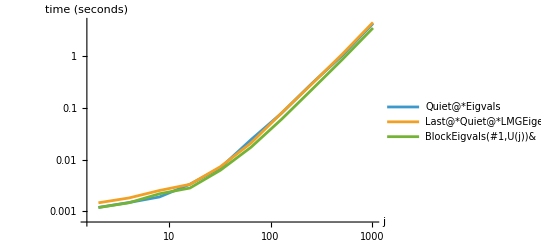

| Quiet@*Eigvals | Last@*Quiet@*LMGEigen | BlockEigvals[#1,U[j]]&
2 | 0.00118236 | 0.00145561 | 0.00117839
4 | 0.0014735 | 0.00180509 | 0.00145657
8 | 0.00188886 | 0.00252003 | 0.00217588
16 | 0.00333113 | 0.00331969 | 0.00281407
32 | 0.00696688 | 0.00730289 | 0.0062364
64 | 0.024346 | 0.0209573 | 0.0173605
128 | 0.0791614 | 0.0800381 | 0.0603748
256 | 0.300665 | 0.295694 | 0.229256
512 | 1.0557 | 1.11996 | 0.880938
1024 | 4.36281 | 4.57486 | 3.56627

```mathematica
ListLogLogPlot[timings,PlotLegends->fns,AxesLabel->{"j","time (seconds)"},PlotRange->All,Joined->True]
timings[[;;,;;,2]]ᵀ//tableHeaded@{js,fns}
```

#### Example Usage:

## Miscellaneous

### PrePrintMatrixForm: Assign to $PrePrint to format matrices automatically

```mathematica
ClearAll[PrePrintMatrixForm]
PrePrintMatrixForm=If[MatrixQ@#,MatrixForm@#,#]&;
```

### Enumerate: Like enumerate in every other language

```mathematica
ClearAll[enumerate]
enumerate=MapIndexed[{#2[[1]],#1}&];
```

### SparseReplaceAll: Like ReplaceAll but works with SparseArrays

```mathematica
(* https://mathematica.stackexchange.com/a/154287 *)
SparseReplaceAll[s_SparseArray,rule_]:=With[{
		elems=ReplaceAll[s["NonzeroValues"],rule],
		default=ReplaceAll[s["Background"],rule]
	},
	SparseArray[
		Automatic,
		s["Dimensions"],
		default,
		{1,{s["RowPointers"],s["ColumnIndices"]},elems}
	]
]
```

#### Example Usage

Say we have a sparse matrix with values μ_i above and below the diagonal:

```mathematica
A=SparseArray[
{
Band[{1,2}]->Array[Subscript[μ, #]&,{3}],
Band[{2,1}]->Array[Subscript[μ, #]&,{3}]
},
{4,4}
]
Eigenvalues[A]
```

SparseArray[…]

{-(√(μ_1^2+μ_2^2+μ_3^2-√(-4 μ_1^2 μ_3^2+(-μ_1^2-μ_2^2-μ_3^2)^2)))/(√2),(√(μ_1^2+μ_2^2+μ_3^2-√(-4 μ_1^2 μ_3^2+(-μ_1^2-μ_2^2-μ_3^2)^2)))/(√2),-(√(μ_1^2+μ_2^2+μ_3^2+√(-4 μ_1^2 μ_3^2+(-μ_1^2-μ_2^2-μ_3^2)^2)))/(√2),(√(μ_1^2+μ_2^2+μ_3^2+√(-4 μ_1^2 μ_3^2+(-μ_1^2-μ_2^2-μ_3^2)^2)))/(√2)}

And we now have specific values of μ_i we want to use:

```mathematica
rules=Array[Subscript[μ, #]->RandomReal[{-10,10}]&,3]
```

{μ_1→9.24832,μ_2→4.20148,μ_3→-8.43884}

The normal replacement doesn’t work!

```mathematica
A/.rules
ReplaceAll[A,rules] (* equivalent to the above *)
Eigenvalues[%]
```

SparseArray[…]

SparseArray[…]

{-(√(μ_1^2+μ_2^2+μ_3^2-√(-4 μ_1^2 μ_3^2+(-μ_1^2-μ_2^2-μ_3^2)^2)))/(√2),(√(μ_1^2+μ_2^2+μ_3^2-√(-4 μ_1^2 μ_3^2+(-μ_1^2-μ_2^2-μ_3^2)^2)))/(√2),-(√(μ_1^2+μ_2^2+μ_3^2+√(-4 μ_1^2 μ_3^2+(-μ_1^2-μ_2^2-μ_3^2)^2)))/(√2),(√(μ_1^2+μ_2^2+μ_3^2+√(-4 μ_1^2 μ_3^2+(-μ_1^2-μ_2^2-μ_3^2)^2)))/(√2)}

So we use SparseReplaceAll instead!

```mathematica
SparseReplaceAll[A,rules]
Eigenvalues[%]
```

SparseArray[…]

{-11.229,11.229,6.95029,-6.95029}

### fMap: Removed, see Comap

### No more laggy/slow chart highlighting!

```mathematica
Charting$InteractiveHighlighting=False;
```

### {list}_seq: Convert a List to a Sequence

```mathematica
Subscript[l_List,seq]:=Sequence@@l
```

#### Example Usage:

```mathematica
f[Subscript[{1,2,3}, seq]]
```

f[1,2,3]

### Benchmark: Compare time taken by different implementations of functions

```mathematica
ClearAll[Benchmark]
Benchmark[fns_List,ns_List,nToInput_]:=Transpose@table[
With[{input=nToInput@n},
Table[{n,RepeatedTiming[fn@nToInput@n][[1]]},{fn,fns}]
],
{n,ns}
]
```

## Strings

### "String with ``"_(sf/st): StringForm/StringTemplate

```mathematica
Subscript[s_String,sf][exprs__]:=StringForm[s,exprs]
Subscript[s_String,st]:=StringTemplate[s]
```

#### Example Usage :

StringForm displays as a string but keeps the StringForm head

```mathematica
Subscript["Hello `` (``)", sf]["World",42]
%//InputForm
```

Hello World (42)

StringForm["Hello `` (``)", "World", 42]

StringTemplate evaluates to a string

```mathematica
Subscript["Hello `` (``)", st]["World",42]
%//FullForm
```

Hello World (42)

"Hello World (42)"

### StringPrepend/StringAppend: Like Prepend/Append, but for Strings.

```mathematica
StringPrepend[rest_,pre_]:=pre<>ToString@rest
StringPrepend[pre_][rest_]:=StringPrepend[rest,pre]

StringAppend[rest_,app_]:=ToString@rest<>app
StringAppend[app_][rest_]:=StingAppend[rest,app]
```

## Scoping

### Eat: Return symbols by name rather than leaking to global scope

```mathematica
ClearAll[Eat]
SetAttributes[Eat,HoldAll]
Eat[symbs_List,body_]:=Block[symbs,body;symbs]
```

```mathematica
leak[val_]:=CoolVariable=val
```

```mathematica
(* This sets CoolVariable in the global scope, so it is 5 after the function *)
leak[5];
CoolVariable
ClearAll[CoolVariable]
```

5

```mathematica
(* Eat the function, so it doesn't assign to the global CoolVariable *)
Eat[{CoolVariable},leak["yummy"]][[1]]
CoolVariable
ClearAll[Dinner,CoolVariable]
```

yummy

CoolVariable

### WithWith: If you’ve ever wanted to nest With’s, this does that nicer :)

Note that this is not needed as of Mathematica 14.2 (?), as With can now take multiple variable specification lists that depend on previous variables.

```mathematica
ClearAll[WithWith]
SetAttributes[WithWith,HoldAll]
WithWith[list_List,body_]:=Fold[
ReplaceAll[{Hold[hinner_],Hold[hvar_]}->Hold@With[{hvar},hinner]]@*List,
Hold@body,
Reverse@First@Map[Hold,Hold@list,{2}]
]//ReleaseHold
```

#### Example Usage

```mathematica
WithWith[{a=3,b=a+1,c2=a^2+b^2,c=√c2},StringForm["Pythagorean theorem: (``)^2+(``)^2=(``)^2",a,b,c]]
```

Pythagorean theorem: (RowBox[{)^2+(RowBox[{)^2=(RowBox[{)^2

equivalent to

```mathematica
With[{a=3},
With[{b=a+1},
With[{c2=a^2+b^2},
With[{c=√c2},
StringForm["Pythagorean theorem: (``)^2+(``)^2=(``)^2",a,b,c]
]
]
]
]
```

Pythagorean theorem: (RowBox[{)^2+(RowBox[{)^2=(RowBox[{)^2

## WIP

### LocalizeAll: Kinda like inverted module?

The idea is to make a scoping function that makes Mathematica behave more like a reasonable language; i.e. rather than having to specify the name of each variable twice (once for the usage and again in the list of local variables), just assume that all variables that appear on the left side of an ‘=’ are local (maybe with a list of exceptions as the first argument?) so each only has to be specified where it is defined.

Note that this is still in the WIP section, but it does *largely* work. There are just a few edge cases it breaks for (notably, setting values using indexing doesn’t work, i.e. list[[index]]=value). Other than that, it does what it should, and so I still use it :)

```mathematica
ClearAll[LocalizeAll];
SetAttributes[LocalizeAll,HoldAll];
LocalizeAll[code_]:=LocalizeAll[{},{},code]
LocalizeAll[extra_List,code_]:=LocalizeAll[extra,{},code]
LocalizeAll[extra_List,except_List,code_]:=Module[{expressions,locals},
expressions=List@@Map[Hold,Hold[code]/.CompoundExpression->List,{2}][[1]];
(*Echo[FullForm@expressions];
Echo[Hold@@Hold[except][[;;]]];*)
locals=Complement[
Join@@Join[
(* lhs=rhs *)
Cases[expressions,
Hold[Set[lhs_,rhs_]]:>Switch[Hold[lhs],
(* {lhs1,lhs2,...}=rhs *)
Hold[_List],Sequence@@Map[Hold,Hold[lhs],{2}][[1]],
(* lhs[[vars]]=lhs *)
Hold[_Part],Hold@@Map[Hold,Hold[lhs],{2}][[1,1]],
(* lhs=rhs *)
_,Hold[lhs]
]
],
(* lhs[vars]:=rhs  TODO: do I also need a Set (not Delayed) for this? *)
Cases[expressions,Hold[SetDelayed[lhs_[vars___],rhs_]]:>Hold@lhs],
(*(* TODO! lhs[[vars]]=lhs *)
Cases[expressions,Hold[Set[lhs_[[vars___]],rhs_]]:>Hold@lhs],*)
(* any extras :) *)
Hold/@extra
],
Hold@@except
]/.Hold[locals__]:>Hold[{locals}];
(*Echo@locals;*)
Module@@Hold[Evaluate[Unevaluated@@locals],code]
]
```

```mathematica
Hold[list[[idx]]]
(*Hold[{l1,l2,l3}]*)
Hold@@Map[Hold,%,{2}]
%[[1,1]]
```

Hold[list⟦idx⟧]

Hold[Hold[list]⟦Hold[idx]⟧]

Hold[list]

```mathematica
list={111,222};
LocalizeAll[{},{list},
list[[3]]=333;
AppendTo[list,555]
]
list
```

Set::noval: Symbol list$24598 in part assignment does not have an immediate value.

AppendTo::rvalue: list$24598 is not a variable with a value, so its value cannot be changed.

AppendTo[list$24598,555]

{111,222}

#### Example

```mathematica
c="C already has a value";
a={1,2};
list={111,222};
ClearAll[e,b]
SetAttributes[hiddenSet,HoldFirst]
hiddenSet[v_Symbol]:=v=ⅇ
returned=LocalizeAll[
{e(* any extra variables to localize, incase they were set indirectly *)},
{b,(* any variables to not localize, incase you want to define some in the gobal scope *)},
a=5+1;
hiddenSet[e];
(*list[[3]]=333;*)
Print[e," ",c," ",d];
{c,d}={1,2};
Print[e," ",c," ",d];
Print["a=",a];
{Mean,Test};
fn[var_]:=var/2;
b=fn[a]+1;
a-b
];
Print[
"returned: should be 2, is: ",returned,
"\na: should be {1,2}, is: ",a,
"\nDownValues@fn: should be {}, is: ",DownValues@fn,
"\ne: should be e, is: ",N@e,
"\nc: should be \"C already has a value\", is: ",c,
"\nd: should be d, is: ",d,
"\nb: should be 4, is: ",b,
"\nlist: should be {111,222,333}, is: ",list
]
```

ⅇ c$25028 d$25028

ⅇ 1 2

a=6

returned: should be 2, is: 2
a: should be {1,2}, is: {1,2}
DownValues@fn: should be {}, is: {}
e: should be e, is: e
c: should be "C already has a value", is: C already has a value
d: should be d, is: d
b: should be 4, is: 4
list: should be {111,222,333}, is: {111,222}

#### Example: if LocalizeAll was implemented using LocalizeAll instead of Module

```mathematica
SetAttributes[localizeAllOuroboros,HoldAll]
localizeAllOuroboros[extra_List,except_List,code_]:=LocalizeAll[{},{},
expressions=List@@Map[Hold,Hold[code]/.CompoundExpression->List,{2}][[1]];
locals=Complement[
Join@@Join[
Cases[expressions,Hold[Set[lhs_,rhs_]]:>Switch[lhs,
_List,Sequence@@Map[Hold,Hold[lhs],{2}][[1]],
_,Hold[lhs]
]],
Cases[expressions,Hold[SetDelayed[lhs_[vars___],rhs_]]:>Hold@lhs],
Hold/@extra
],
Hold@@except
]/.Hold[locals__]:>Hold[{locals}];
Module@@Hold[Evaluate[Unevaluated@@locals],code]
]
localizeAllOuroboros[{},{},a=2;a]
a
(* All of the local variables should be undefined still: *)
expressions
locals
```

2

3

expressions

locals

#### Example: timings, compared to Module

```mathematica
ClearAll[b]
RepeatedTiming[
LocalizeAll[{e},{b},
a=5+1;
hiddenSet[e];
{c,d}={1,2};
(*Print[e," ",c," ",d];
Print["a=",a];*)
{Mean,Test};
fn[var_]:=var/2;
b=fn[a]+1;
a-b
]
]
ClearAll[b]
RepeatedTiming[
Module[{a,e,c,d,fb},
a=5+1;
hiddenSet[e];
{c,d}={1,2};
(*Print[e," ",c," ",d];
Print["a=",a];*)
{Mean,Test};
fn[var_]:=var/2;
b=fn[a]+1;
a-b
]
]
```

{0.000081897,2}

{0.0000158109,2}